```mathematica
SetDirectory["/home/tony/Research"];
<<AbaciSymmetricFunctions.m
<<MatrixRSK.m
```

```mathematica
TableForm/@Reverse/@MatrixRSK[{{1,0,2,3},{3,2,1,1},{0,0,3,1}}]
```

{3 | 3 | 4 | 4 | 4 | 4 |  |  |  |  | 
1 | 1 | 1 | 1 | 2 | 2 | 3 | 3 | 3 | 3 | 4,2 | 2 | 2 | 2 | 2 | 3 |  |  |  |  | 
1 | 1 | 1 | 1 | 1 | 1 | 2 | 2 | 3 | 3 | 3}

```mathematica
MatrixForm@SchurToPower[4]
```

(1/4 | -1/4 | 0 | 1/4 | -1/4
1/3 | 0 | -1/3 | 0 | 1/3
1/8 | -1/8 | 1/4 | -1/8 | 1/8
1/4 | 1/4 | 0 | -1/4 | -1/4
1/24 | 1/8 | 1/12 | 1/8 | 1/24)

```mathematica
IntegerPartitions@12
```

{{12},{11,1},{10,2},{10,1,1},{9,3},{9,2,1},{9,1,1,1},{8,4},{8,3,1},{8,2,2},{8,2,1,1},{8,1,1,1,1},{7,5},{7,4,1},{7,3,2},{7,3,1,1},{7,2,2,1},{7,2,1,1,1},{7,1,1,1,1,1},{6,6},{6,5,1},{6,4,2},{6,4,1,1},{6,3,3},{6,3,2,1},{6,3,1,1,1},{6,2,2,2},{6,2,2,1,1},{6,2,1,1,1,1},{6,1,1,1,1,1,1},{5,5,2},{5,5,1,1},{5,4,3},{5,4,2,1},{5,4,1,1,1},{5,3,3,1},{5,3,2,2},{5,3,2,1,1},{5,3,1,1,1,1},{5,2,2,2,1},{5,2,2,1,1,1},{5,2,1,1,1,1,1},{5,1,1,1,1,1,1,1},{4,4,4},{4,4,3,1},{4,4,2,2},{4,4,2,1,1},{4,4,1,1,1,1},{4,3,3,2},{4,3,3,1,1},{4,3,2,2,1},{4,3,2,1,1,1},{4,3,1,1,1,1,1},{4,2,2,2,2},{4,2,2,2,1,1},{4,2,2,1,1,1,1},{4,2,1,1,1,1,1,1},{4,1,1,1,1,1,1,1,1},{3,3,3,3},{3,3,3,2,1},{3,3,3,1,1,1},{3,3,2,2,2},{3,3,2,2,1,1},{3,3,2,1,1,1,1},{3,3,1,1,1,1,1,1},{3,2,2,2,2,1},{3,2,2,2,1,1,1},{3,2,2,1,1,1,1,1},{3,2,1,1,1,1,1,1,1},{3,1,1,1,1,1,1,1,1,1},{2,2,2,2,2,2},{2,2,2,2,2,1,1},{2,2,2,2,1,1,1,1},{2,2,2,1,1,1,1,1,1},{2,2,1,1,1,1,1,1,1,1},{2,1,1,1,1,1,1,1,1,1,1},{1,1,1,1,1,1,1,1,1,1,1,1}}

```mathematica
χ[{10,10,10,10},{10,10,5,5,5,3,1,1}]
```

-18

```mathematica
MatrixForm@PowerToSchur[10]
```

(1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1
-1 | 0 | -1 | 1 | -1 | 0 | 2 | -1 | 0 | -1 | 1 | 3 | -1 | 0 | -1 | 1 | 0 | 2 | 4 | -1 | 1 | -1 | 0 | 2 | -1 | 1 | 3 | 5 | 0 | -1 | 1 | 3 | 0 | 2 | 4 | 6 | -1 | 1 | 3 | 5 | 7 | 9
0 | -1 | 1 | -1 | 0 | 0 | 0 | 0 | -1 | 2 | 0 | 2 | 0 | -1 | 1 | -1 | 1 | 1 | 5 | 1 | -1 | 0 | 0 | 0 | 3 | 1 | 3 | 9 | -1 | 2 | 0 | 2 | 2 | 2 | 6 | 14 | 5 | 3 | 5 | 11 | 21 | 35
1 | 0 | 0 | 0 | 1 | -1 | 1 | 1 | 0 | -1 | -1 | 3 | 1 | 0 | 0 | 0 | -2 | 0 | 6 | 0 | 0 | 1 | -1 | 1 | -2 | -2 | 2 | 10 | 0 | -1 | -1 | 3 | -3 | -1 | 5 | 15 | -4 | -4 | 0 | 8 | 20 | 36
0 | 0 | -1 | -1 | 1 | 0 | -2 | 0 | 1 | -2 | 0 | -2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | -1 | 2 | 1 | -1 | -3 | 1 | 1 | 5 | 3 | 0 | 2 | 0 | 1 | 3 | 5 | 15 | -5 | 3 | 7 | 15 | 35 | 75
0 | 1 | 0 | 0 | -1 | 1 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | -1 | -1 | 1 | -1 | 5 | 0 | 0 | -2 | 0 | -2 | 0 | 0 | 0 | 16 | -2 | -2 | -2 | -2 | 0 | -2 | 4 | 34 | 0 | 0 | 0 | 16 | 64 | 160
-1 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 1 | 1 | -1 | 1 | -1 | 0 | 1 | 1 | 0 | -2 | 4 | 0 | 0 | 1 | 1 | 1 | 2 | -2 | -2 | 10 | 3 | 3 | 1 | 3 | 1 | -3 | 1 | 21 | 4 | -4 | -8 | 0 | 28 | 84
0 | 0 | 0 | 0 | -1 | -1 | -1 | 1 | 0 | 1 | -1 | -3 | 0 | 1 | -1 | 1 | -1 | -1 | -5 | 2 | 2 | -1 | 0 | 2 | 4 | 0 | 0 | -4 | 0 | -1 | 1 | 3 | 0 | 2 | 4 | 6 | 10 | 2 | 6 | 14 | 34 | 90
0 | 0 | 1 | 1 | 0 | 0 | 0 | -1 | 0 | 1 | 1 | -3 | 0 | -1 | 1 | 1 | -1 | 1 | -5 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | 0 | 1 | 1 | -3 | -3 | 1 | 1 | 21 | -5 | -5 | 3 | 19 | 91 | 315
0 | 0 | -1 | 1 | 1 | -1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 1 | 2 | -1 | -1 | 3 | 1 | -1 | 5 | 0 | 2 | -2 | -6 | 3 | -1 | -5 | 15 | 15 | 9 | 3 | 5 | 55 | 225
0 | -1 | 0 | 0 | 0 | 0 | 0 | 1 | -1 | -1 | 1 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 | 2 | 1 | 1 | 1 | -2 | 2 | -2 | 10 | -1 | -1 | 1 | -1 | -1 | -1 | -5 | 35 | -10 | -2 | -10 | -10 | 70 | 350
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | -1 | -1 | 1 | 1 | -1 | 1 | -2 | -2 | -2 | -1 | 1 | 0 | 0 | -4 | 4 | 0 | -2 | 2 | 6 | 3 | 1 | -1 | 21 | 6 | 6 | -6 | -14 | 14 | 126
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | -1 | -1 | -1 | -1 | 2 | 1 | 2 | 0 | 1 | -1 | -3 | -2 | 2 | -1 | 0 | 2 | -4 | 0 | 0 | -4 | -3 | 3 | -1 | 3 | 2 | 0 | 2 | 0 | -10 | 2 | 2 | 6 | 14 | 42
0 | 0 | 0 | 0 | 1 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | -2 | -1 | -1 | -1 | 1 | -1 | -7 | 0 | 0 | 2 | 0 | 2 | 0 | 0 | 0 | -16 | 0 | -2 | -2 | 6 | 0 | -2 | 4 | -6 | 0 | 0 | 0 | 16 | 64 | 288
0 | 0 | 0 | 0 | -1 | 0 | 2 | 1 | 0 | -1 | -1 | 3 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 | -2 | -1 | 1 | -1 | -2 | -2 | -2 | -10 | 0 | 1 | 1 | -3 | 3 | 1 | -5 | -15 | -10 | 2 | 6 | 10 | 70 | 450
0 | 0 | -1 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 | 1 | 0 | 0 | 1 | 3 | -3 | -1 | -1 | 0 | 0 | 0 | 3 | -1 | 3 | -9 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 15 | -9 | -9 | -9 | 63 | 567
0 | 0 | 1 | -1 | 0 | 0 | 0 | -1 | 1 | 1 | -1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 1 | -1 | 0 | 2 | -1 | 1 | 3 | 5 | 3 | -3 | -1 | -3 | -2 | 0 | -10 | 0 | -5 | 5 | 7 | -15 | 35 | 525
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -2 | 0 | 0 | -2 | -2 | 0 | -2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -2 | 4 | 0 | 4 | 0 | 4 | 0 | 28 | 0 | 0 | 0 | -32 | 0 | 448
-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 2 | -2 | 2 | -1 | -1 | 0 | 0 | -4 | -4 | 0 | -2 | -2 | 6 | -3 | 1 | 1 | 21 | -6 | 6 | 6 | -14 | -14 | 126
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | -1 | 1 | 3 | 2 | 0 | 1 | -1 | -2 | -2 | 2 | 0 | 0 | -1 | 1 | -1 | 2 | 2 | -2 | -10 | 0 | -1 | 1 | 3 | -3 | -1 | 1 | -21 | 20 | 4 | 0 | 8 | 28 | 252
0 | 0 | 0 | 0 | -1 | -1 | -1 | 1 | 1 | 1 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | -1 | -1 | -2 | 2 | 2 | -10 | 3 | 3 | -1 | 3 | 1 | -3 | 5 | -15 | -20 | 4 | -8 | 0 | 20 | 300
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 2 | 0 | 2 | 0 | 1 | -1 | -1 | 1 | -1 | 5 | -2 | 2 | 2 | -1 | -1 | 0 | 0 | -4 | -4 | 3 | 0 | 2 | 0 | -1 | 3 | -1 | -21 | -10 | -6 | 2 | 6 | 14 | 210
0 | 0 | 0 | 0 | 1 | 0 | -2 | 0 | 0 | 0 | 0 | 0 | -2 | 0 | 0 | 2 | 0 | 0 | 8 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -6 | 0 | 0 | 0 | 0 | 0 | 0 | -48 | 0 | 0 | 0 | 0 | 0 | 768
0 | 0 | 1 | 1 | 0 | 0 | 0 | -1 | -1 | -1 | -1 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 1 | 0 | -2 | -1 | -1 | 3 | -5 | 3 | -3 | 1 | -3 | 2 | 0 | 10 | 0 | 5 | 5 | -7 | -15 | -35 | 525
0 | 0 | 0 | 0 | -1 | 1 | -1 | 1 | -1 | -1 | 1 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | -1 | 1 | -2 | -2 | 2 | 10 | 3 | 3 | 1 | 3 | -1 | -3 | -5 | -15 | 20 | 4 | 8 | 0 | -20 | 300
0 | 0 | -1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 | -1 | 0 | 0 | 1 | -3 | -3 | 1 | -1 | 0 | 0 | 0 | 3 | 1 | 3 | 9 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -15 | -9 | 9 | -9 | -63 | 567
0 | -1 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 1 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -2 | 2 | -1 | 1 | -1 | -2 | -2 | -2 | -10 | -1 | -1 | -1 | -1 | 1 | -1 | 5 | 35 | 10 | -2 | 10 | -10 | -70 | 350
1 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | -1 | -1 | -1 | -1 | -1 | 0 | -1 | 1 | 0 | 2 | 4 | 0 | 0 | -1 | 1 | -1 | 2 | 2 | -2 | -10 | 3 | 3 | -1 | 3 | -1 | -3 | -1 | 21 | -4 | -4 | 8 | 0 | -28 | 84
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | -2 | 0 | -2 | 0 | -1 | 1 | -1 | 1 | 1 | 5 | 2 | 2 | -2 | -1 | 1 | 0 | 0 | -4 | 4 | 3 | 0 | -2 | 0 | 1 | 3 | 1 | -21 | 10 | -6 | -2 | 6 | -14 | 210
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 1 | 1 | -3 | 2 | 0 | -1 | -1 | -2 | 2 | 2 | 0 | 0 | 1 | 1 | 1 | 2 | -2 | -2 | 10 | 0 | -1 | -1 | 3 | 3 | -1 | -1 | -21 | -20 | 4 | 0 | 8 | -28 | 252
0 | 0 | 0 | 0 | -1 | 0 | 2 | 1 | 0 | 1 | -1 | -3 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -2 | -2 | 1 | 1 | 1 | -2 | 2 | -2 | 10 | 0 | 1 | -1 | -3 | -3 | 1 | 5 | -15 | 10 | 2 | -6 | 10 | -70 | 450
0 | 0 | -1 | -1 | 1 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | -2 | -1 | 1 | 3 | -1 | -1 | -5 | 0 | 2 | 2 | -6 | -3 | -1 | 5 | 15 | -15 | 9 | -3 | 5 | -55 | 225
0 | 0 | 0 | 0 | 1 | -1 | 1 | 0 | 0 | 0 | 0 | 0 | -2 | 1 | 1 | -1 | 1 | 1 | -7 | 0 | 0 | -2 | 0 | -2 | 0 | 0 | 0 | 16 | 0 | -2 | 2 | 6 | 0 | -2 | -4 | -6 | 0 | 0 | 0 | 16 | -64 | 288
0 | 0 | 1 | -1 | 0 | 0 | 0 | -1 | 0 | -1 | 1 | 3 | 0 | 1 | -1 | 1 | -1 | -1 | -5 | 1 | -1 | 1 | -1 | 1 | -1 | 1 | -1 | 1 | 0 | 1 | -1 | -3 | 3 | 1 | -1 | 21 | 5 | -5 | -3 | 19 | -91 | 315
0 | 1 | 0 | 0 | -1 | -1 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 1 | -1 | 1 | 1 | 5 | 0 | 0 | 2 | 0 | 2 | 0 | 0 | 0 | -16 | -2 | -2 | 2 | -2 | 0 | -2 | -4 | 34 | 0 | 0 | 0 | 16 | -64 | 160
-1 | 0 | 0 | 0 | 1 | 1 | 1 | 1 | 0 | 1 | -1 | -3 | 1 | 0 | 0 | 0 | -2 | 0 | 6 | 0 | 0 | -1 | -1 | -1 | -2 | 2 | 2 | -10 | 0 | -1 | 1 | 3 | 3 | -1 | -5 | 15 | 4 | -4 | 0 | 8 | -20 | 36
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 1 | 1 | -1 | 1 | 2 | -1 | -2 | 0 | 1 | 1 | -3 | 2 | 2 | 1 | 0 | -2 | -4 | 0 | 0 | 4 | -3 | 3 | 1 | 3 | -2 | 0 | -2 | 0 | 10 | 2 | -2 | 6 | -14 | 42
0 | 0 | 0 | 0 | -1 | 1 | -1 | 1 | 0 | -1 | -1 | 3 | 0 | -1 | 1 | 1 | -1 | 1 | -5 | -2 | 2 | 1 | 0 | -2 | 4 | 0 | 0 | 4 | 0 | -1 | -1 | 3 | 0 | 2 | -4 | 6 | -10 | 2 | -6 | 14 | -34 | 90
0 | 0 | -1 | 1 | 1 | 0 | -2 | 0 | -1 | 2 | 0 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | -1 | -2 | 1 | 1 | -3 | -1 | 1 | -5 | 3 | 0 | -2 | 0 | -1 | 3 | -5 | 15 | 5 | 3 | -7 | 15 | -35 | 75
0 | -1 | 1 | 1 | 0 | 0 | 0 | 0 | 1 | -2 | 0 | -2 | 0 | 1 | -1 | -1 | 1 | -1 | 5 | -1 | -1 | 0 | 0 | 0 | 3 | -1 | 3 | -9 | -1 | 2 | 0 | 2 | -2 | 2 | -6 | 14 | -5 | 3 | -5 | 11 | -21 | 35
1 | 0 | -1 | -1 | -1 | 0 | 2 | -1 | 0 | 1 | 1 | -3 | -1 | 0 | 1 | 1 | 0 | -2 | 4 | 1 | 1 | 1 | 0 | -2 | -1 | -1 | 3 | -5 | 0 | -1 | -1 | 3 | 0 | 2 | -4 | 6 | 1 | 1 | -3 | 5 | -7 | 9
-1 | 1 | 1 | -1 | 1 | -1 | 1 | 1 | -1 | -1 | 1 | -1 | 1 | -1 | -1 | 1 | 1 | -1 | 1 | -1 | 1 | -1 | 1 | -1 | 1 | -1 | 1 | -1 | 1 | 1 | -1 | 1 | -1 | 1 | -1 | 1 | -1 | 1 | -1 | 1 | -1 | 1)

```mathematica
HomogeneousToPower[4]//MatrixForm
```

(1/4 | 0 | 0 | 0 | 0
1/3 | 1/3 | 0 | 0 | 0
1/8 | 0 | 1/4 | 0 | 0
1/4 | 1/2 | 1/2 | 1/2 | 0
1/24 | 1/6 | 1/4 | 1/2 | 1)

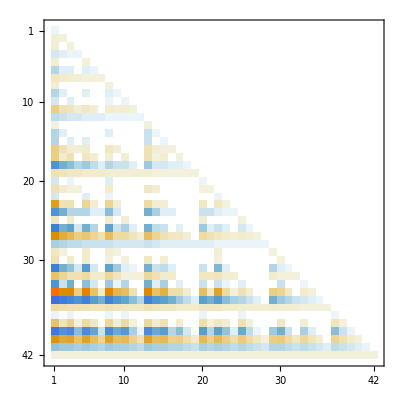
{-Graphics-,-Graphics-}

```mathematica
{HomogeneousToElementary[10]//MatrixPlot,ElementaryToHomogeneous[10]//MatrixPlot}
```

```mathematica
ElementaryToPower[12]//MatrixPlot
```

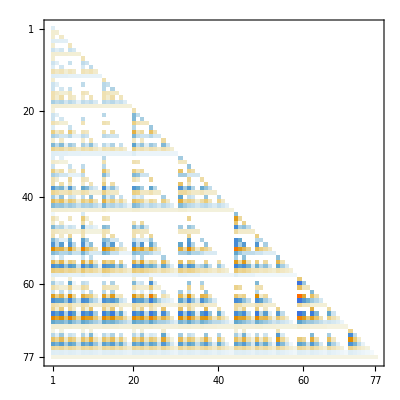

```mathematica
PowerToElementary[12]//MatrixPlot
```